## Importing and definitions

```mathematica
SetDirectory[NotebookDirectory[]];
Get["../Mathematica_packages/QMB.wl"]
```

```mathematica
Parity[ψ_,L_]:=ψ[[FromDigits[Reverse[#],2]+1&/@Tuples[{0,1},L]]]
```

```mathematica
ClearAll[ParityMatrix];ParityMatrix[L_]:=Normal@SparseArray[{FromDigits[#,2]+1,FromDigits[Reverse[#],2]+1}->1.&/@Tuples[{0,1},L]]
```

## Global parameters

```mathematica
(*Subscript[h, x]: magnetic field in x direction. L: number of spins*)
{hx,L}={1.,11}
```

{1.,11}

## Mean level spacing ratio (r_n)(h_z/h_x,J/h_x)

### Single

```mathematica
SortBy[Select[MeanLevelSpacingRatioData,#[[1]]==0.01&],#[[2]]&]
```

{{0.01,0.01,0.353427},{0.01,0.02,0.379699},{0.01,0.03,0.406734},{0.01,0.04,0.429054},{0.01,0.06,0.426594},{0.01,0.07,0.422336},{0.01,0.08,0.420608},{0.01,0.09,0.448161},{0.01,0.11,0.408424},{0.01,0.12,0.443104},{0.01,0.13,0.422237},{0.01,0.14,0.387188},{0.01,0.16,0.373297},{0.01,0.17,0.376144},{0.01,0.18,0.330376},{0.01,0.19,0.371827},{0.01,0.21,0.42232},{0.01,0.22,0.408056},{0.01,0.23,0.357279},{0.01,0.24,0.366624},{0.01,0.26,0.427637},{0.01,0.27,0.406158},{0.01,0.28,0.459745},{0.01,0.29,0.436054},{0.01,0.31,0.355395},{0.01,0.32,0.282751},{0.01,0.33,0.386485},{0.01,0.34,0.407647},{0.01,0.36,0.390472},{0.01,0.37,0.357766},{0.01,0.38,0.413055},{0.01,0.39,0.397963},{0.01,0.41,0.42481},{0.01,0.42,0.405814},{0.01,0.43,0.406325},{0.01,0.44,0.449284},{0.01,0.46,0.362063},{0.01,0.47,0.407136},{0.01,0.48,0.385663},{0.01,0.49,0.398059},{0.01,0.51,0.35294},{0.01,0.52,0.386477},{0.01,0.53,0.352562},{0.01,0.54,0.410176},{0.01,0.56,0.450542},{0.01,0.57,0.387153},{0.01,0.58,0.433471},{0.01,0.59,0.446705},{0.01,0.61,0.398805},{0.01,0.62,0.449026},{0.01,0.63,0.394545},{0.01,0.64,0.42016},{0.01,0.66,0.347699},{0.01,0.67,0.415167},{0.01,0.68,0.439781},{0.01,0.69,0.396467},{0.01,0.71,0.397382},{0.01,0.72,0.364233},{0.01,0.73,0.411983},{0.01,0.74,0.408981},{0.01,0.76,0.374921},{0.01,0.77,0.423724},{0.01,0.78,0.425647},{0.01,0.79,0.443047},{0.01,0.81,0.381842},{0.01,0.82,0.460368},{0.01,0.83,0.452965},{0.01,0.84,0.398808},{0.01,0.86,0.393456},{0.01,0.87,0.445932},{0.01,0.88,0.442853},{0.01,0.89,0.462706},{0.01,0.91,0.452167},{0.01,0.92,0.441358},{0.01,0.93,0.41308},{0.01,0.94,0.408182},{0.01,0.96,0.453472},{0.01,0.97,0.459103},{0.01,0.98,0.370808},{0.01,0.99,0.465527},{0.01,1.01,0.398937},{0.01,1.02,0.430442},{0.01,1.03,0.429925},{0.01,1.04,0.417496},{0.01,1.06,0.376606},{0.01,1.07,0.434552},{0.01,1.08,0.394154},{0.01,1.09,0.37567},{0.01,1.11,0.410654},{0.01,1.12,0.393684},{0.01,1.13,0.381475},{0.01,1.14,0.410263},{0.01,1.16,0.444343},{0.01,1.17,0.42777},{0.01,1.18,0.430791},{0.01,1.19,0.434664},{0.01,1.21,0.405357},{0.01,1.22,0.436152},{0.01,1.23,0.443049},{0.01,1.24,0.435725},{0.01,1.26,0.398437},{0.01,1.27,0.422505},{0.01,1.28,0.389036},{0.01,1.29,0.392906},{0.01,1.31,0.431983},{0.01,1.32,0.456923},{0.01,1.33,0.408849},{0.01,1.34,0.396315},{0.01,1.36,0.43102},{0.01,1.37,0.451554},{0.01,1.38,0.452668},{0.01,1.39,0.423765},{0.01,1.41,0.413793},{0.01,1.42,0.442183},{0.01,1.43,0.457477},{0.01,1.44,0.427128},{0.01,1.46,0.398149},{0.01,1.47,0.394468},{0.01,1.48,0.387938},{0.01,1.49,0.418586},{0.01,1.51,0.404809},{0.01,1.52,0.421626},{0.01,1.53,0.429028},{0.01,1.54,0.415996},{0.01,1.56,0.389293},{0.01,1.57,0.415106},{0.01,1.58,0.376251},{0.01,1.59,0.426372},{0.01,1.61,0.389281},{0.01,1.62,0.385157},{0.01,1.63,0.387989},{0.01,1.64,0.407713},{0.01,1.66,0.4051},{0.01,1.67,0.389866},{0.01,1.68,0.419745},{0.01,1.69,0.407673},{0.01,1.71,0.40706},{0.01,1.72,0.428094},{0.01,1.73,0.432513},{0.01,1.74,0.411114},{0.01,1.76,0.398101},{0.01,1.77,0.407724},{0.01,1.78,0.441834},{0.01,1.79,0.391533},{0.01,1.81,0.367428},{0.01,1.82,0.413771},{0.01,1.83,0.39887},{0.01,1.84,0.417493},{0.01,1.86,0.435077},{0.01,1.87,0.413912},{0.01,1.88,0.424366},{0.01,1.89,0.416665},{0.01,1.91,0.381597},{0.01,1.92,0.394073},{0.01,1.93,0.409308},{0.01,1.94,0.403016},{0.01,1.96,0.427299},{0.01,1.97,0.454393},{0.01,1.98,0.413856},{0.01,1.99,0.395643},{0.01,2.01,0.435834},{0.01,2.02,0.403785},{0.01,2.03,0.421308},{0.01,2.04,0.44001},{0.01,2.06,0.402058},{0.01,2.07,0.409373},{0.01,2.08,0.416699},{0.01,2.09,0.370891},{0.01,2.11,0.384031},{0.01,2.12,0.404135},{0.01,2.13,0.400962},{0.01,2.14,0.389998},{0.01,2.16,0.414703},{0.01,2.17,0.445806},{0.01,2.18,0.418566},{0.01,2.19,0.411836},{0.01,2.21,0.384629},{0.01,2.22,0.412741},{0.01,2.23,0.385835},{0.01,2.24,0.428333},{0.01,2.26,0.43278},{0.01,2.27,0.374849},{0.01,2.28,0.425984},{0.01,2.29,0.42712},{0.01,2.31,0.445611},{0.01,2.32,0.431161},{0.01,2.33,0.424553},{0.01,2.34,0.427638},{0.01,2.36,0.434833},{0.01,2.37,0.414935},{0.01,2.38,0.46106},{0.01,2.39,0.398956},{0.01,2.41,0.407952},{0.01,2.42,0.398702},{0.01,2.43,0.397291},{0.01,2.44,0.411205},{0.01,2.46,0.420524},{0.01,2.47,0.439807},{0.01,2.48,0.374024},{0.01,2.49,0.390272},{0.01,2.51,0.389333},{0.01,2.52,0.393568},{0.01,2.53,0.416545},{0.01,2.54,0.39464},{0.01,2.56,0.365177},{0.01,2.57,0.378426},{0.01,2.58,0.386213},{0.01,2.59,0.379592},{0.01,2.61,0.409465},{0.01,2.62,0.409113},{0.01,2.63,0.391431},{0.01,2.64,0.397326},{0.01,2.66,0.378969},{0.01,2.67,0.412457},{0.01,2.68,0.400428},{0.01,2.69,0.393287},{0.01,2.71,0.382},{0.01,2.72,0.391292},{0.01,2.73,0.408117},{0.01,2.74,0.422882},{0.01,2.76,0.413099},{0.01,2.77,0.428509},{0.01,2.78,0.425499},{0.01,2.79,0.420487},{0.01,2.81,0.419027},{0.01,2.82,0.434156},{0.01,2.83,0.448582},{0.01,2.84,0.425773},{0.01,2.86,0.415317},{0.01,2.87,0.428108},{0.01,2.88,0.430447},{0.01,2.89,0.458213},{0.01,2.91,0.425798},{0.01,2.92,0.414796},{0.01,2.93,0.412659},{0.01,2.94,0.416668},{0.01,2.96,0.401966},{0.01,2.97,0.382345},{0.01,2.98,0.393153},{0.01,2.99,0.357033}}

```mathematica
{hz,J}={0.01,0.32};
H=IsingNNOpenHamiltonian[hx,hz,ConstantArray[J,L-1],L];
{eigVals,eigVecs}=Transpose[Sort[Transpose[Eigensystem[H]]]];
{EvenEigVals,evenEigenVecs}={eigVals[[#]],eigVecs[[#]]}&[Flatten[Position[Round[ParallelMap[Braket[#,Parity[#,L]]&,eigVecs],10.^0],1.]]];
OddEigVals=Complement[eigVals,EvenEigVals];
OddEigVecs=Complement[eigVecs,evenEigenVecs];
{MeanLevelSpacingRatio[OddEigVals],MeanLevelSpacingRatio[EvenEigVals]}
```

{0.312133,0.282751}

```mathematica
EvenEigVals=#[[Ceiling[0.05Length[#]];;-Ceiling[0.05Length[#]]]]&[EvenEigVals];
OddEigVals=#[[Ceiling[0.05Length[#]];;-Ceiling[0.05Length[#]]]]&[OddEigVals];
```

```mathematica
iprs=ParallelTable[Total[Abs[i]^4],{i,eigVecs}];
```

```mathematica
iprsEven=ParallelTable[Total[Abs[i]^4],{i,evenEigenVecs}];
```

```mathematica
iprsOdd=ParallelTable[Total[Abs[i]^4],{i,OddEigVecs}];
```

```mathematica
1/2^11.
```

0.000488281

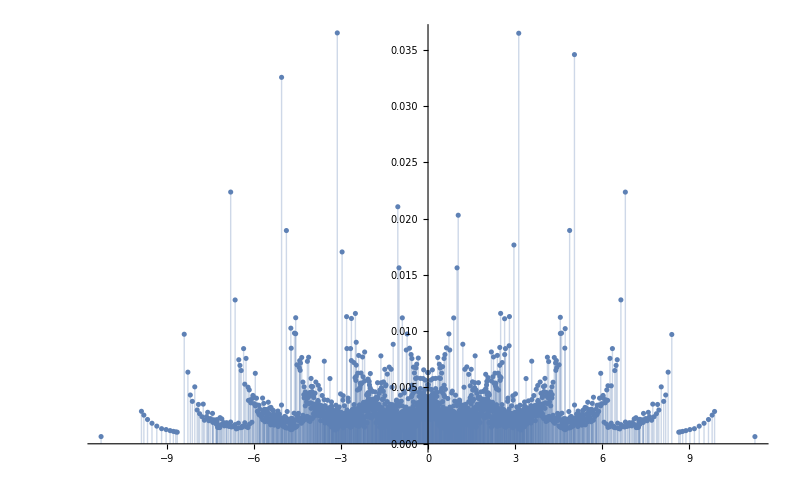
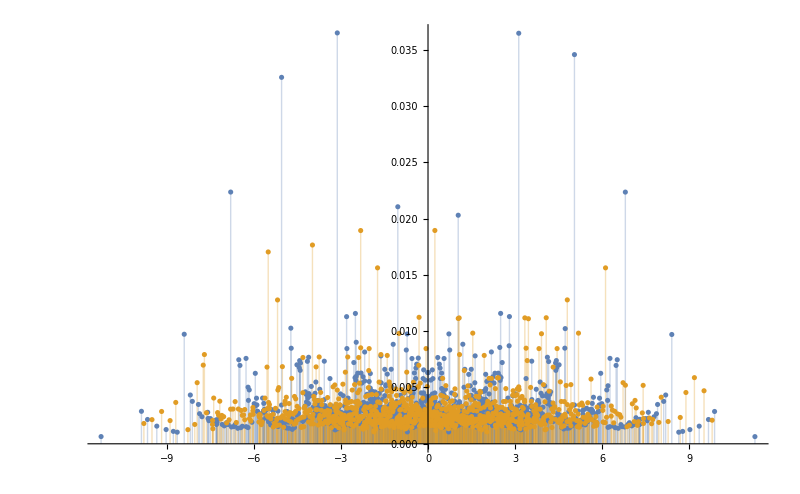

```mathematica
{ListPlot[Transpose[{eigVals,iprs}],PlotRange->All,Filling->Axis,ImageSize->800],ListPlot[{Transpose[{EvenEigVals,iprsEven}],Transpose[{OddEigVals,iprsOdd}]},PlotRange->All,Filling->Axis,ImageSize->800]}
```

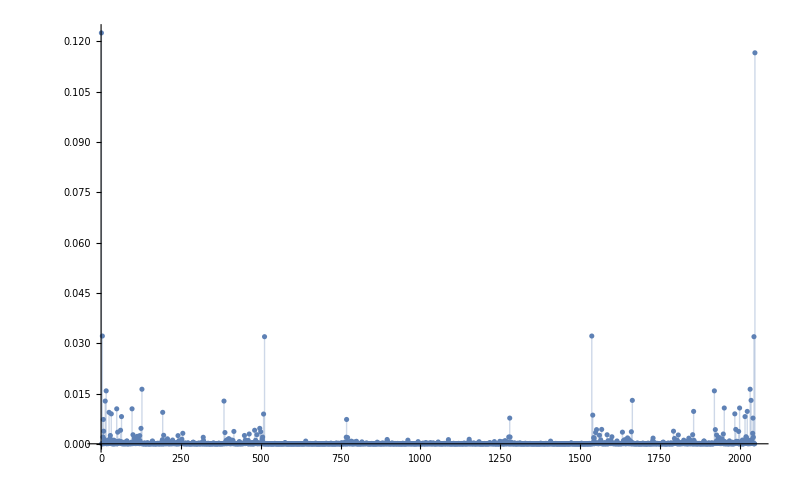
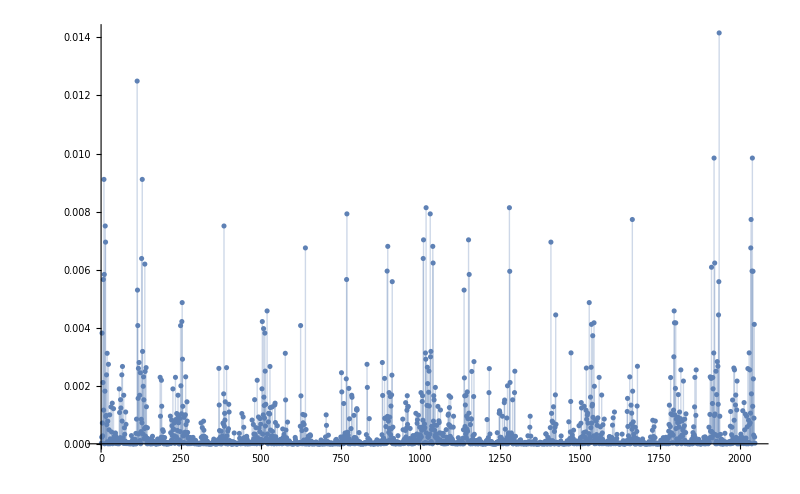

```mathematica
{ListPlot[Abs[eigVecs[[390]]]^2,PlotRange->All,Filling->Axis,ImageSize->800],ListPlot[Abs[eigVecs[[88]]]^2,PlotRange->All,Filling->Axis,ImageSize->800]}
```

```mathematica
DuplicateFreeQ[EvenEigVals]
```

True

```mathematica
{MeanLevelSpacingRatio[OddEigVals],MeanLevelSpacingRatio[EvenEigVals]}
```

{0.298113,0.264786}

```mathematica
Length[EvenEigVals]
```

952

```mathematica
Length[OddEigVals]
```

894

### To compute the whole diagram

```mathematica
missingValues=Complement[Round[Flatten[Table[{i,j},{i,0.01,3,0.01},{j,0.01,3,0.01}],1],10.^-2],Round[MeanLevelSpacingRatioData[[2;;,{1,2}]],10.^-3]]
```

```mathematica
DateString[]
```

```mathematica
(*Parece que tarda 2.05~2.1 s por iteración, debería tardar approx 41 min*)
AbsoluteTiming[
Do[
Module[
{H,eigVals,eigVecs,EvenEigVals,hz,J},
{hz,J}=hzJ;
H=IsingNNOpenHamiltonian[hx,hz,ConstantArray[J,L-1],L];
{eigVals,eigVecs}=Transpose[Sort[Transpose[Eigensystem[H]]]];
EvenEigVals=eigVals[[Flatten[Position[Round[ParallelMap[Braket[#,Parity[#,L]]&,eigVecs],10.^0],1.]]]];
AppendTo[MeanLevelSpacingRatioData,{hz,J,MeanLevelSpacingRatio[EvenEigVals]}];
],{hzJ,missingValues}
]
]
```

{28125.8,Null}

```mathematica
MeanLevelSpacingRatioData[[1]]
```

{h_z/h_x,J/h_x,<r_n>}

```mathematica
90000-74953
```

15047

```mathematica
1.6*28800/3600
```

12.8

```mathematica
DateString[]
```

Fri 23 Aug 2024 17:38:16

```mathematica
MeanLevelSpacingRatioData=Import["data/mean_level_spacing_ratio/wisniacki_open_L_11_hx_1.csv","CSV"];
```

```mathematica
fontSize=18;
fig=
ListDensityPlot[MeanLevelSpacingRatioData[[2;;]](*para excluir el primer elemento {hz/hx, J/hx, <r_n>}*),
InterpolationOrder->0,
ColorFunction->"SunsetColors",
PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"⟨r_n⟩",LabelStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black]],Automatic],
Frame->True,
FrameStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black],
FrameLabel->{"h_z / h_x","J / h_x"}]
```

-Graphics-

## Export data and figure

```mathematica
(*Data*)
Export["/home/jadeleon/Documents/quantum_chaotic_channels/numerica_JA/mean_level_spacing_ratio.csv",MeanLevelSpacingRatioData,"CSV"]
```

/home/jadeleon/Documents/quantum_chaotic_channels/numerica_JA/mean_level_spacing_ratio.csv

```mathematica
(*Figure*)
Export["/home/jadeleon/Documents/quantum_chaotic_channels/mean_level_spacing_ratio.png",fig,"PNG",ImageResolution->300]
```

/home/jadeleon/Documents/quantum_chaotic_channels/mean_level_spacing_ratio.png

## Mean level spacing ratio (r_n)(h_z/h_x,J/h_x) no se que es

```mathematica
L=11;{hx,hz,J}={1,0.5,1.};
(*se iba a tardar 20+ min*)
AbsoluteTiming[
Module[{H,eveneigenvecs,oddeigenvecs},
H=IsingNNOpenHamiltonian[hx,hz,ConstantArray[J,L-1],L];
{eveneigenvecs,oddeigenvecs}=ParityEigenvectors[L];
(*Even symmetric Hamiltonian*)
(*Heven=ParallelTable[Braket[a,b],{a,eveneigenvecs},{b,H.#&/@eveneigenvecs}];*)
c=H.#&/@eveneigenvecs;
Heven=Table[Braket[a,#]&/@c,{a,eveneigenvecs}];
]
]
```

{279.056,Null}

```mathematica
Sort[#]==#&[Eigenvalues[Heven]]
```

False

```mathematica
MeanLevelSpacingRatio[Sort[Eigenvalues[Heven]]]
```

0.520833

```mathematica
0.25*1056/60
```

4.4

## Wisniacki open, L=7, paridad +1

```mathematica
?MeanLevelSpacingRatio
```

```mathematica
{#[[1]],energies=#[[2;;,3;;]];}&[Import["data/energies/wisniacki_open/L_7/parity_plus1_hz_and_J_from_0_to_2_step_0.1.csv"]]
```

{{hz,J,E0,...,En, con n la dimension del subespacio},Null}

```mathematica
energies[[1]]
```

{-7.,-5.,-5.,-5.,-5.,-3.,-3.,-3.,-3.,-3.,-3.,-3.,-3.,-3.,-3.,-3.,-3.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,5.,5.,5.,5.,7.}

```mathematica
meanR=If[Head[#]===Real,#,0.]&/@(MeanLevelSpacingRatio/@energies[[;;,8;;-8]]);
```

Divide::indet: Indeterminate expression 0./0. encountered.

Divide::infy: Infinite expression (4.44089×10^-16)/0. encountered.

Divide::infy: Infinite expression (8.88178×10^-16)/0. encountered.

Divide::infy: Infinite expression (1.33227×10^-15)/0. encountered.

General::stop: Further output of Divide::infy will be suppressed during this calculation.

Divide::indet: Indeterminate expression 0./0. encountered.

General::stop: Further output of Divide::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Min::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Min::nord will be suppressed during this calculation.

```mathematica
meanR=Flatten[Table[{Subdivide[0.,2.,20][[i]],Subdivide[0.,2.,20][[j]],meanR[[21*(i-1)+j]]},{i,21},{j,21}],1];
```

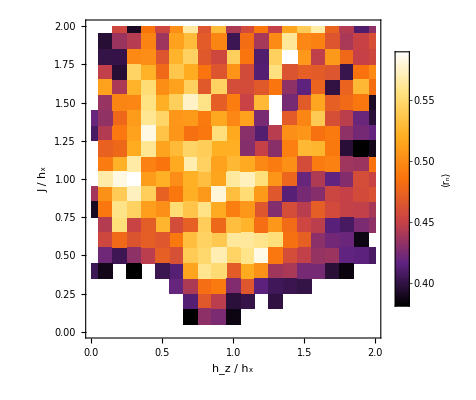

```mathematica
fontSize=22;

fig=ListDensityPlot[meanR,
ColorFunction->"SunsetColors",ColorFunctionScaling->True,
PlotRange->{0.38,0.6},
InterpolationOrder->0,
PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"⟨r_n⟩",LabelStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black]],Automatic],
Frame->True,
FrameStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black],
FrameLabel->{"h_z / h_x","J / h_x"}
]
```

```mathematica
Export["figs_ja/tmp/mean_level_spacing_ratio_wisniacki_open_L_7.png",fig,"PNG"]
```

figs_ja/tmp/mean_level_spacing_ratio_wisniacki_open_L_7.png